# Reymann 2016

{0.00148113,{x→-1.}}

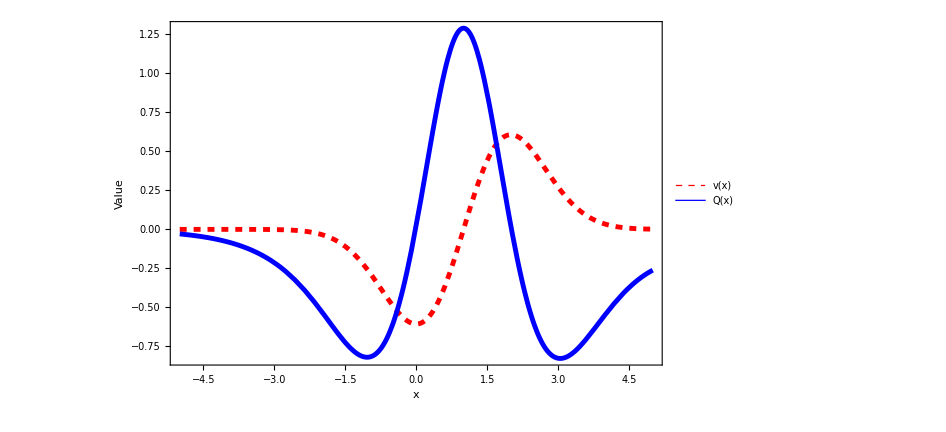

/home/soumyadeep/Desktop/Active Gel/My_codes/Pseudocleavage.pdf

Export::chtype: First argument FileNameJoin[{/home/soumyadeep/Desktop/Active Gel/My_codes,Pseudocleavage.jpg,ImageResolution→600}] is not a valid file specification.

$Failed

```mathematica
a=-1;
v[x_] :=- (x-a) Exp[-0.5*(x-a)^2];
l=1;
τ=1;
β=10;
ode=l^2 Q''[x]-τ v[x] Q'[x]-Q[x]==(β* τ/2) D[v[x],x];
sol=NDSolve[{ode,Q[-10]==0,Q[10]==0},Q,{x,-5,5}];
(*Dsolve[ode, Q[x], x]*)
(*Plot[Evaluate[Q'[x]/.sol],{x,-5,5}, PlotRange->All,AxesLabel->{"x","Q'(x)"},PlotLabel->"Numerical Solution Q'(x)"];*)
Qprime[x_]:=Evaluate[Q'[x]/.First[sol]];
NMaximize[{Qprime[x],-1≤x≤1},x]

plt=Plot[{v[x],Evaluate[Q[x]/.First[sol]]},{x,5,-5},ScalingFunctions->{"Reverse",None},PlotRange->All,PlotLegends->Placed[{"v(x)","Q(x)"},Above],PlotStyle->{{Red, Thickness[0.005], Dashed},{Blue, Thickness[0.005]}},AxesOrigin->{0,0},Frame->True,FrameLabel->{"x","Value"}, ImageSize->700,  FrameStyle->Directive[Black,Thickness[0.005]], LabelStyle->25]
Export[FileNameJoin[{"/home/soumyadeep/Desktop/Active Gel/My_codes","Pseudocleavage.pdf"}],plt]
```

{1.0691,{x→0.146711}}

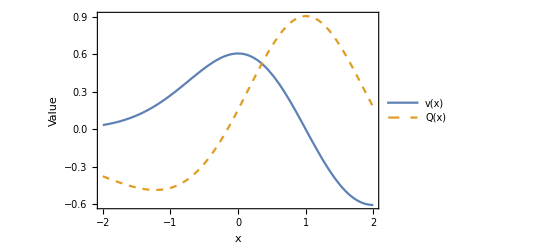

```mathematica
a=1;
v[x_] := -(x-a) Exp[-0.5*(x-a)^2];
l=1;
τ=0.5;
β=10;
λ=0.5;
ode=l^2 Q''[x]-τ v[x] Q'[x]-Q[x]+λ Q[x]==(β τ/2) D[v[x],x];
sol=NDSolve[{ode,Q[-5]==0,Q[5]==0},Q,{x,-5,5}];
(*Plot[Evaluate[Q[x]/.sol],{x,-5,5},PlotRange->All,AxesLabel->{"x","Q(x)"},PlotLabel->"Numerical Solution Q(x)"]*)
(*Dsolve[ode, Q[x], x]*)
(*Plot[Evaluate[Q'[x]/.sol],{x,-5,5}, PlotRange->All,AxesLabel->{"x","Q'(x)"},PlotLabel->"Numerical Solution Q'(x)"]*)
Qprime[x_]:=Evaluate[Q'[x]/.First[sol]];
NMaximize[{Qprime[x],-1≤x≤1},x]
Plot[{v[x],Evaluate[Q[x]/.First[sol]]},{x,-2,2},PlotRange->All,PlotLegends->Placed[{"v(x)","Q(x)"},Above],PlotStyle->{{Thick},{Thick,Dashed},{Thick,Red}},Frame->True,FrameLabel->{"x","Value"}]
```